```mathematica
a=0; b=6; n=4;
```

```mathematica
h = (b-a)/n
```

3/2

```mathematica
XDT={}; YDT={};
```

```mathematica
For[i=0, i≤n, i++,
	xdata[i]=a+i*h;
	ydata[i]=N[(√21*Sin[3*xdata[i]^2/28])/(√(2+xdata[i]^2+√((4+xdata[i]^2)^3)))];
	XDT=Append[XDT,xdata[i]];
	YDT=Append[YDT, ydata[i]];];
```

```mathematica
MatrixForm[XDT]MatrixForm[YDT]
```

(0
3/2
3
9/2
6) (0.
0.245407
0.494946
0.318015
-0.176239)

```mathematica
Array[xdata,{n+1,0}]; Array[ydata,{n+1,0}];
```

```mathematica
ex=∑_(i=0)^n xdata[i];ey=∑_(i=0)^n ydata[i];exx=∑_(i=0)^n xdata[i]^2;
```

```mathematica
exy=∑_(i=0)^n xdata[i]*ydata[i]; eyy=∑_(i=0)^n ydata[i]^2;
```

```mathematica
a= (ey*exx-ex*exy)/((n+1)*exx-ex^2);b=((n+1)*exy-ex*ey)/((n+1)*exx-ex^2);
```

```mathematica
g[x_]:=a+b*x;
```

```mathematica
g[x]
```

0.2324-0.018658 x

```mathematica
data = Table[{N[xdata[i]], N[ydata[i]]},{i,0,n}]
```

{{0.,0.},{1.5,0.245407},{3.,0.494946},{4.5,0.318015},{6.,-0.176239}}

```mathematica
Clear[a, b]; rules= FindFit[data,a+b*x,{a,b},x]; y=a+b*x/.rules
```

0.2324-0.018658 x

```mathematica
gr1:=Plot[N[(√21*Sin[3 x^2/28])/(√(2+x^2+√((4+x^2)^3)))],{x, 0,6}];
```

```mathematica
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
```

```mathematica
gr3:=Plot[y,{x, 0,6}];
```

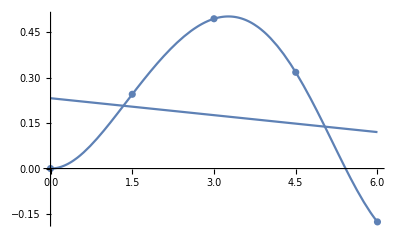

```mathematica
Show[{gr1,gr2,gr3}]
```

```mathematica
r=((n+1)*exy-ex*ey)/(√((n+1)*exx-ex^2)* √((n+1)*eyy-ey^2))
```

-0.166731